```mathematica
ClearAll["Global`*"]
```

```mathematica
ab0={{{266.7430375647669,5.3669490770725385},{266.2864313471503,5.361241499352332}},{{261.3924870466322,5.367567195595854},{260.23882772020727,5.360646454015543}},{{247.72101683937825,5.369173818005181},{247.44656735751295,5.358243199481865}},{{238.4273801813472,5.369253359779792},{238.38487694300522,5.357472069300518}},{{228.56298575129534,5.369698429404145},{228.72328367875645,5.356702153497409}},{{208.86334196891195,5.370952882124352},{208.75647668393785,5.3546170660621755}},{{178.53060233160625,5.374293636658031},{179.15236398963734,5.352065657383419}},{{137.88293393782385,5.376197781735751},{138.62856217616584,5.3480181347150255}},{{90.68976683937825,5.378783193005181},{90.29630829015545,5.343864961139896}},{{67.29841321243524,5.378891272668394},{67.39313471502592,5.3425752914507765}},{{63.05051813471503,5.378292584196891},{62.57448186528497,5.342342130829015}},{{55.85168393782384,5.378307156735751},{55.97555051813472,5.342355488989637}},{{52.271696891191716,5.37855731865285},{51.805375647668406,5.3427283031088075}},{{45.014572538860115,5.377843264248704},{45.81606217616581,5.342861884715026}}};
a0=ab0[[;;,1,;;]];
b0=ab0[[;;,2,;;]];
ab0//MatrixForm
a0//MatrixForm
b0//MatrixForm
```

((266.743
5.36695) | (266.286
5.36124)
(261.392
5.36757) | (260.239
5.36065)
(247.721
5.36917) | (247.447
5.35824)
(238.427
5.36925) | (238.385
5.35747)
(228.563
5.3697) | (228.723
5.3567)
(208.863
5.37095) | (208.756
5.35462)
(178.531
5.37429) | (179.152
5.35207)
(137.883
5.3762) | (138.629
5.34802)
(90.6898
5.37878) | (90.2963
5.34386)
(67.2984
5.37889) | (67.3931
5.34258)
(63.0505
5.37829) | (62.5745
5.34234)
(55.8517
5.37831) | (55.9756
5.34236)
(52.2717
5.37856) | (51.8054
5.34273)
(45.0146
5.37784) | (45.8161
5.34286))

(266.743 | 5.36695
261.392 | 5.36757
247.721 | 5.36917
238.427 | 5.36925
228.563 | 5.3697
208.863 | 5.37095
178.531 | 5.37429
137.883 | 5.3762
90.6898 | 5.37878
67.2984 | 5.37889
63.0505 | 5.37829
55.8517 | 5.37831
52.2717 | 5.37856
45.0146 | 5.37784)

(266.286 | 5.36124
260.239 | 5.36065
247.447 | 5.35824
238.385 | 5.35747
228.723 | 5.3567
208.756 | 5.35462
179.152 | 5.35207
138.629 | 5.34802
90.2963 | 5.34386
67.3931 | 5.34258
62.5745 | 5.34234
55.9756 | 5.34236
51.8054 | 5.34273
45.8161 | 5.34286)

```mathematica
aT={{258.15009715025917,5.364537321891191},{247.9420336787565,5.364436528497409},{238.91434585492232,5.364090430699481},{229.31590025906735,5.364109860751295},{208.86091321243526,5.363422522668394},{179.45595854922283,5.363360589378238},{138.57512953367876,5.362350226683938},{98.29420336787567,5.361338649611398},{80.28740284974094,5.361253643134715}}
```

{{258.15,5.36454},{247.942,5.36444},{238.914,5.36409},{229.316,5.36411},{208.861,5.36342},{179.456,5.36336},{138.575,5.36235},{98.2942,5.36134},{80.2874,5.36125}}

```mathematica
Sqrt[a0*b0]
```

{{266.515,5.36409},{260.815,5.36411},{247.584,5.36371},{238.406,5.36336},{228.643,5.3632},{208.81,5.36278},{178.841,5.36317},{138.255,5.36209},{90.4928,5.3613},{67.3458,5.3607},{62.812,5.36029},{55.9136,5.3603},{52.038,5.36061},{45.4135,5.36032}}

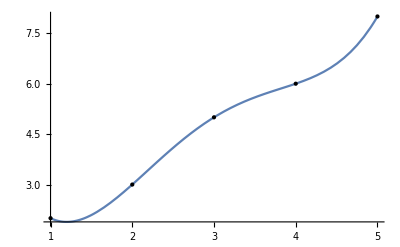

```mathematica
(*In this section we define Interpolation*)
(*Define the data points*)data={{1,2},{2,3},{3,5},{4,6},{5,8}};

(*Perform piecewise linear interpolation*)
interp=Interpolation[data,InterpolationOrder->4];

(*Plot the interpolated curve*)
Plot[interp[x],{x,1,5},Epilog->{PointSize[Medium],Point[data]}]
```

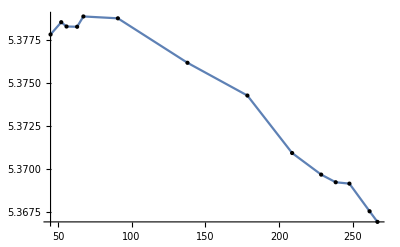

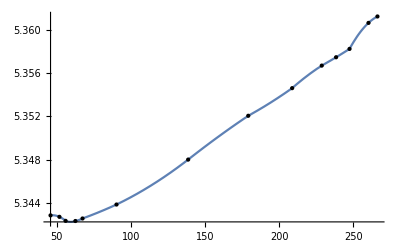

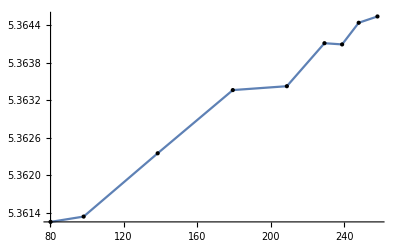

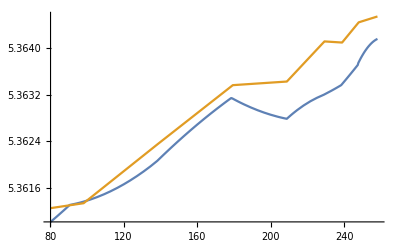

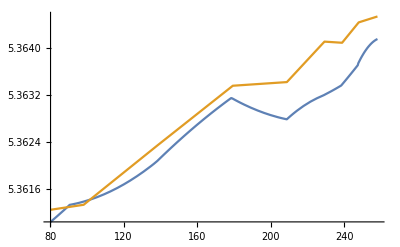

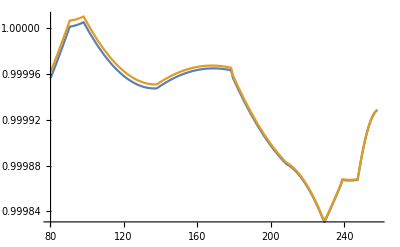

```mathematica
(*In this section, we check if a_T has volume conservation*)
interpa0=Interpolation[a0,InterpolationOrder->1];
Plot[interpa0[x],{x,a0[[14,1]],a0[[1,1]]},Epilog->{PointSize[Medium],Point[a0]}](*The 14 is the length so that we pick beginning and end temp of the plot*)
interpb0=Interpolation[b0,InterpolationOrder->2];
Plot[interpb0[x],{x,b0[[14,1]],b0[[1,1]]},Epilog->{PointSize[Medium],Point[b0]}](*The 14 is the length so that we pick beginning and end temp of the plot*)
interpaT=Interpolation[aT,InterpolationOrder->1];
Plot[interpaT[x],{x,aT[[9,1]],aT[[1,1]]},Epilog->{PointSize[Medium],Point[aT]}](*The 14 is the length so that we pick beginning and end temp of the plot*)
Plot[{Sqrt[interpa0[x]*interpb0[x]],interpaT[x]},{x,aT[[9,1]],aT[[1,1]]}]
Plot[{(interpa0[x]+interpb0[x])/2,interpaT[x]},{x,aT[[9,1]],aT[[1,1]]}]
Plot[{Sqrt[interpa0[x]*interpb0[x]]/interpaT[x],((interpa0[x]+interpb0[x])/2)/interpaT[x]},{x,aT[[9,1]],aT[[1,1]]}]
```